# Densities for paper 3

```mathematica
corr[{n1_,m1_},{n2_,m2_},τ_:τ]:=If[EvenQ[n1+n2]∧EvenQ[m1+m2],((-1)^(n1+m1)ⅈ^(n1+m1+n2+m2)Subscript[τ, 1/2(n1+m1+n2+m2)]^2)/(2π)(2Gamma[1/2(1+n1+n2)]Gamma[1/2(1+m1+m2)])/Gamma[1+1/2(n1+m1+n2+m2)],0]
p[Y_,M_]:=Exp[-1/2 Y.Inverse[M].Y]/(√((2π)^Length[M] Det[M]))
pre[M_]:=1/(√((2π)^Length[M] Det[M]))

Cov[correlations_,τ_:τ]:=Table[corr[i,j,τ],{i,correlations},{j,correlations}]
```

```mathematica
FullSimplify[p[{T11, T12,T22},Cov[{{2,0},{1,1},{0,2}}]],Assumptions->Subscript[τ, 2]>0]
```

(2 √2 ⅇ^(-(3 T11^2+8 T12^2-2 T11 T22+3 T22^2)/(2 τ_2^2)))/(π^(3/2) τ_2^3)

### Covariance matrices

```mathematica
MatrixForm[Cov[{
{1,0},{3,0},{1,2},{5,0},{3,2},{1,4},
{0,1},{0,3},{2,1},{4,1},{2,3},{0,5},

{0,0},{2,0},{0,2},{4,0},{2,2},{0,4},
{1,1},{3,1},{1,3}}]]
```

(τ_1^2/2 | -(3 τ_2^2)/8 | -τ_2^2/8 | (5 τ_3^2)/16 | τ_3^2/16 | τ_3^2/16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(3 τ_2^2)/8 | (5 τ_3^2)/16 | τ_3^2/16 | -(35 τ_4^2)/128 | -(5 τ_4^2)/128 | -(3 τ_4^2)/128 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-τ_2^2/8 | τ_3^2/16 | τ_3^2/16 | -(5 τ_4^2)/128 | -(3 τ_4^2)/128 | -(5 τ_4^2)/128 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(5 τ_3^2)/16 | -(35 τ_4^2)/128 | -(5 τ_4^2)/128 | (63 τ_5^2)/256 | (7 τ_5^2)/256 | (3 τ_5^2)/256 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
τ_3^2/16 | -(5 τ_4^2)/128 | -(3 τ_4^2)/128 | (7 τ_5^2)/256 | (3 τ_5^2)/256 | (3 τ_5^2)/256 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
τ_3^2/16 | -(3 τ_4^2)/128 | -(5 τ_4^2)/128 | (3 τ_5^2)/256 | (3 τ_5^2)/256 | (7 τ_5^2)/256 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | τ_1^2/2 | -(3 τ_2^2)/8 | -τ_2^2/8 | τ_3^2/16 | τ_3^2/16 | (5 τ_3^2)/16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(3 τ_2^2)/8 | (5 τ_3^2)/16 | τ_3^2/16 | -(3 τ_4^2)/128 | -(5 τ_4^2)/128 | -(35 τ_4^2)/128 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -τ_2^2/8 | τ_3^2/16 | τ_3^2/16 | -(5 τ_4^2)/128 | -(3 τ_4^2)/128 | -(5 τ_4^2)/128 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | τ_3^2/16 | -(3 τ_4^2)/128 | -(5 τ_4^2)/128 | (7 τ_5^2)/256 | (3 τ_5^2)/256 | (3 τ_5^2)/256 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | τ_3^2/16 | -(5 τ_4^2)/128 | -(3 τ_4^2)/128 | (3 τ_5^2)/256 | (3 τ_5^2)/256 | (7 τ_5^2)/256 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (5 τ_3^2)/16 | -(35 τ_4^2)/128 | -(5 τ_4^2)/128 | (3 τ_5^2)/256 | (7 τ_5^2)/256 | (63 τ_5^2)/256 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | τ_0^2 | -τ_1^2/2 | -τ_1^2/2 | (3 τ_2^2)/8 | τ_2^2/8 | (3 τ_2^2)/8 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -τ_1^2/2 | (3 τ_2^2)/8 | τ_2^2/8 | -(5 τ_3^2)/16 | -τ_3^2/16 | -τ_3^2/16 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -τ_1^2/2 | τ_2^2/8 | (3 τ_2^2)/8 | -τ_3^2/16 | -τ_3^2/16 | -(5 τ_3^2)/16 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (3 τ_2^2)/8 | -(5 τ_3^2)/16 | -τ_3^2/16 | (35 τ_4^2)/128 | (5 τ_4^2)/128 | (3 τ_4^2)/128 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | τ_2^2/8 | -τ_3^2/16 | -τ_3^2/16 | (5 τ_4^2)/128 | (3 τ_4^2)/128 | (5 τ_4^2)/128 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (3 τ_2^2)/8 | -τ_3^2/16 | -(5 τ_3^2)/16 | (3 τ_4^2)/128 | (5 τ_4^2)/128 | (35 τ_4^2)/128 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | τ_2^2/8 | -τ_3^2/16 | -τ_3^2/16
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -τ_3^2/16 | (5 τ_4^2)/128 | (3 τ_4^2)/128
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -τ_3^2/16 | (3 τ_4^2)/128 | (5 τ_4^2)/128)

```mathematica
Grid[{{
MatrixForm[Cov[{{1,0},{3,0},{1,2},{5,0},{3,2},{1,4}}]],
MatrixForm[Cov[{{0,1},{0,3},{2,1},{4,1},{2,3},{0,5}}]],
MatrixForm[Cov[{{0,0},{2,0},{0,2},{4,0},{2,2},{0,4}}]],
MatrixForm[Cov[{{1,1},{3,1},{1,3}}]]}}]
```

(τ_1^2/2 | -(3 τ_2^2)/8 | -τ_2^2/8 | (5 τ_3^2)/16 | τ_3^2/16 | τ_3^2/16
-(3 τ_2^2)/8 | (5 τ_3^2)/16 | τ_3^2/16 | -(35 τ_4^2)/128 | -(5 τ_4^2)/128 | -(3 τ_4^2)/128
-τ_2^2/8 | τ_3^2/16 | τ_3^2/16 | -(5 τ_4^2)/128 | -(3 τ_4^2)/128 | -(5 τ_4^2)/128
(5 τ_3^2)/16 | -(35 τ_4^2)/128 | -(5 τ_4^2)/128 | (63 τ_5^2)/256 | (7 τ_5^2)/256 | (3 τ_5^2)/256
τ_3^2/16 | -(5 τ_4^2)/128 | -(3 τ_4^2)/128 | (7 τ_5^2)/256 | (3 τ_5^2)/256 | (3 τ_5^2)/256
τ_3^2/16 | -(3 τ_4^2)/128 | -(5 τ_4^2)/128 | (3 τ_5^2)/256 | (3 τ_5^2)/256 | (7 τ_5^2)/256) | (τ_1^2/2 | -(3 τ_2^2)/8 | -τ_2^2/8 | τ_3^2/16 | τ_3^2/16 | (5 τ_3^2)/16
-(3 τ_2^2)/8 | (5 τ_3^2)/16 | τ_3^2/16 | -(3 τ_4^2)/128 | -(5 τ_4^2)/128 | -(35 τ_4^2)/128
-τ_2^2/8 | τ_3^2/16 | τ_3^2/16 | -(5 τ_4^2)/128 | -(3 τ_4^2)/128 | -(5 τ_4^2)/128
τ_3^2/16 | -(3 τ_4^2)/128 | -(5 τ_4^2)/128 | (7 τ_5^2)/256 | (3 τ_5^2)/256 | (3 τ_5^2)/256
τ_3^2/16 | -(5 τ_4^2)/128 | -(3 τ_4^2)/128 | (3 τ_5^2)/256 | (3 τ_5^2)/256 | (7 τ_5^2)/256
(5 τ_3^2)/16 | -(35 τ_4^2)/128 | -(5 τ_4^2)/128 | (3 τ_5^2)/256 | (7 τ_5^2)/256 | (63 τ_5^2)/256) | (τ_0^2 | -τ_1^2/2 | -τ_1^2/2 | (3 τ_2^2)/8 | τ_2^2/8 | (3 τ_2^2)/8
-τ_1^2/2 | (3 τ_2^2)/8 | τ_2^2/8 | -(5 τ_3^2)/16 | -τ_3^2/16 | -τ_3^2/16
-τ_1^2/2 | τ_2^2/8 | (3 τ_2^2)/8 | -τ_3^2/16 | -τ_3^2/16 | -(5 τ_3^2)/16
(3 τ_2^2)/8 | -(5 τ_3^2)/16 | -τ_3^2/16 | (35 τ_4^2)/128 | (5 τ_4^2)/128 | (3 τ_4^2)/128
τ_2^2/8 | -τ_3^2/16 | -τ_3^2/16 | (5 τ_4^2)/128 | (3 τ_4^2)/128 | (5 τ_4^2)/128
(3 τ_2^2)/8 | -τ_3^2/16 | -(5 τ_3^2)/16 | (3 τ_4^2)/128 | (5 τ_4^2)/128 | (35 τ_4^2)/128) | (τ_2^2/8 | -τ_3^2/16 | -τ_3^2/16
-τ_3^2/16 | (5 τ_4^2)/128 | (3 τ_4^2)/128
-τ_3^2/16 | (3 τ_4^2)/128 | (5 τ_4^2)/128)

## Critical points

### Critical points δ

```mathematica
moments={Subscript[σ, 0]->7.2588,Subscript[σ, 1]->40.974,Subscript[σ, 2]->285.905,Subscript[σ, 3]->2269.1};
```

(σ_0^2 | 0 | 0 | -σ_1^2/2 | -σ_1^2/2 | 0
0 | σ_1^2/2 | 0 | 0 | 0 | 0
0 | 0 | σ_1^2/2 | 0 | 0 | 0
-σ_1^2/2 | 0 | 0 | (3 σ_2^2)/8 | σ_2^2/8 | 0
-σ_1^2/2 | 0 | 0 | σ_2^2/8 | (3 σ_2^2)/8 | 0
0 | 0 | 0 | 0 | 0 | σ_2^2/8)

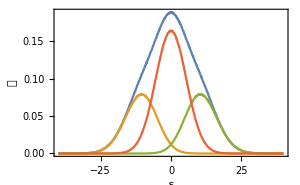

```mathematica
MatrixForm[Mtot=Cov[{{0,0},{1,0},{0,1},{2,0},{0,2},{1,1}},σ]]
MatrixForm[Mmc=Cov[{{0,0},{2,0},{0,2},{1,1}},σ]/.moments];
α=(pre[Mtot]/pre[Mmc])/.moments;

Δ=0.1;
nsamples=100000000;

random=RandomVariate[MultinormalDistribution[Mmc],nsamples];
det=random⟦All,2⟧random⟦All,3⟧-random⟦All,4⟧^2;
tr=random⟦All,2⟧+random⟦All,3⟧;

compCrit={random⟦All,1⟧,Abs[det]}ᵀ;
Ncritical=α/(Δ nsamples)Total[BinLists[compCrit⟦All,1⟧->compCrit⟦All,2⟧,{-40,40,Δ}],{2}];
Clear[compCrit];

compMax={random⟦All,1⟧,HeavisideTheta[-tr]HeavisideTheta[det]Abs[det]}ᵀ;
Nmax=α/(Δ nsamples)Total[BinLists[compMax⟦All,1⟧->compMax⟦All,2⟧,{-40,40,Δ}],{2}];
Clear[compMax];

compMin={random⟦All,1⟧,HeavisideTheta[tr]HeavisideTheta[det]Abs[det]}ᵀ;
Nmin=α/(Δ nsamples)Total[BinLists[compMin⟦All,1⟧->compMin⟦All,2⟧,{-40,40,Δ}],{2}];
Clear[compMin];

compSaddle={random⟦All,1⟧,HeavisideTheta[-det]Abs[det]}ᵀ;
Nsaddle=α/(Δ nsamples)Total[BinLists[compSaddle⟦All,1⟧->compSaddle⟦All,2⟧,{-40,40,Δ}],{2}];
Clear[compSaddle];

Clear[random];Clear[det];Clear[tr];

ListLinePlot[{Ncritical,Nmin,Nmax,Nsaddle},DataRange->{-40,40},ImageSize->300,Frame->True,FrameLabel->{"δ","𝒩"}]
```

```mathematica
(*Y={T,T1,T2,T11,T12,T22};
MatrixForm[M=Cov[{{0,0},{1,0},{0,1},{2,0},{1,1},{0,2}}]]
p[{T_,T1_,T2_,T11_,T12_,T22_}]=FullSimplify[Exp[-1/2Y.Inverse[M].Y]/(√((2π)^Length[M] Det[M]))];

data=ParallelTable[
Quiet[NIntegrate[Abs[T11 T22 -T12^2]p[{T,0,0,T11,T12,T22}]/.{Subscript[τ, 0]->1,Subscript[τ, 1]->1/2,Subscript[τ, 2]->1/3},{T11,-∞,∞},{T12,-∞,∞},{T22,-∞,∞}]]
,{T,-4,4,0.1}];
dataMin=ParallelTable[
Quiet[NIntegrate[

HeavisideTheta[1/2 (T11+T22+√(T11^2+4 T12^2-2 T11 T22+T22^2))]
HeavisideTheta[1/2 (T11+T22-√(T11^2+4 T12^2-2 T11 T22+T22^2))]
Abs[T11 T22 -T12^2]p[{T,0,0,T11,T12,T22}]/.{Subscript[τ, 0]->1,Subscript[τ, 1]->1/2,Subscript[τ, 2]->1/3},{T11,-∞,∞},{T12,-∞,∞},{T22,-∞,∞}]]
,{T,-4,4,0.1}];
dataMax=ParallelTable[
Quiet[NIntegrate[

HeavisideTheta[-1/2 (T11+T22+√(T11^2+4 T12^2-2 T11 T22+T22^2))]
HeavisideTheta[-1/2 (T11+T22-√(T11^2+4 T12^2-2 T11 T22+T22^2))]
Abs[T11 T22 -T12^2]p[{T,0,0,T11,T12,T22}]/.{Subscript[τ, 0]->1,Subscript[τ, 1]->1/2,Subscript[τ, 2]->1/3},{T11,-∞,∞},{T12,-∞,∞},{T22,-∞,∞}]]
,{T,-4,4,0.1}];
dataSad=ParallelTable[
Quiet[NIntegrate[

HeavisideTheta[-1/2 (T11+T22+√(T11^2+4 T12^2-2 T11 T22+T22^2))1/2 (T11+T22-√(T11^2+4 T12^2-2 T11 T22+T22^2))]
Abs[T11 T22 -T12^2]p[{T,0,0,T11,T12,T22}]/.{Subscript[τ, 0]->1,Subscript[τ, 1]->1/2,Subscript[τ, 2]->1/3},{T11,-∞,∞},{T12,-∞,∞},{T22,-∞,∞}]]
,{T,-4,4,0.1}];
ListLinePlot[{data,dataMin,dataMax,dataSad},DataRange->{-4,4}]*)
```

### λ_1 and λ_2 critical points

```mathematica
(*moments={Subscript[τ, 0]->1,Subscript[τ, 1]->1.7991650071290282,Subscript[τ, 2]->7.258798160002886,Subscript[τ, 3]->40.973950702143256,Subscript[τ, 4]->285.90540786740746,Subscript[τ, 5]->2269.103396361828};*)
moments={Subscript[τ, 0]->1,Subscript[τ, 1]->1.76201,Subscript[τ, 2]->7.02844,Subscript[τ, 3]->40.1639,Subscript[τ, 4]->281.132,Subscript[τ, 5]->2257.73};
```

```mathematica
(*moments={Subscript[τ, 0]->1.,Subscript[τ, 1]->2.8284271247461903,Subscript[τ, 2]->8.,Subscript[τ, 3]->39.191835884530846,Subscript[τ, 4]->247.8709341572747,Subscript[τ, 5]->1854.896223512248};*)
```

```mathematica
MatrixForm[Mtot=Cov[{{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{4,0},{3,1},{2,2}}]/.moments];
MatrixForm[Mmc=Cov[{{2,0},{0,2},{1,2},{4,0},{3,1},{2,2}}]/.moments];

α=(pre[Mtot]/pre[Mmc]);
```

```mathematica
(*MatrixForm[Mtot=Cov[{{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{4,0},{3,1},{2,2}}]];
MatrixForm[Mmc=Cov[{{2,0},{0,2},{1,2},{4,0},{3,1},{2,2}}]];
FullSimplify[(-1/2{T11,0,T22,0,0,T122,T1111,T1112,T1122}.Inverse[Mtot].{T11,0,T22,0,0,T122,T1111,T1112,T1122})-(-1/2{T11,T22,T122,T1111,T1112,T1122}.Inverse[Mmc].{T11,T22,T122,T1111,T1112,T1122})]*)
```

```mathematica
Exp[-(2 T122^2)/Subscript[τ, 3]^2+(256 T1112^2 Subscript[τ, 3]^4)/(20 Subscript[τ, 3]^4 Subscript[τ, 4]^2-25 Subscript[τ, 2]^2 Subscript[τ, 4]^4)]/.moments
```

ⅇ^(-0.000184995 T1112^2-0.00123982 T122^2)

```mathematica
Integrate[Exp[-1/2{T11,T22,T122,T1111,T1112,T1122}.Inverse[Mmc].{T11,T22,T122,T1111,T1112,T1122}]
,{T11,-∞,∞},{T22,-∞,T11},{T122,-∞,∞},{T1111,-∞,∞},{T1112,-∞,∞},{T1122,-∞,∞}]
```

3.30078×10^9

```mathematica
1/2 √((2π)^Length[Mmc] Det[Mmc])
```

3.30078×10^9

```mathematica
Δ=0.1;
nsamples=10000000;

random=Select[RandomVariate[MultinormalDistribution[Mmc],nsamples],#⟦1⟧≥ #⟦2⟧&];
det=random⟦All,4⟧(random⟦All,6⟧+(2 random⟦All,3⟧^2)/(random⟦All,1⟧-random⟦All,2⟧))-random⟦All,5⟧^2;
tr=random⟦All,4⟧+(random⟦All,6⟧+(2 random⟦All,3⟧^2)/(random⟦All,1⟧-random⟦All,2⟧));
```

```mathematica
compCrit={random⟦All,1⟧,π/2 Abs[det](random⟦All,1⟧-random⟦All,2⟧)ⅇ^(-0.0001720612145297022 random⟦All,5⟧^2-0.0011912812724415717 random⟦All,3⟧^2)}ᵀ;
Ncritical=α/(Δ Length[compCrit])Total[BinLists[compCrit⟦All,1⟧->compCrit⟦All,2⟧,{-40,40,Δ}],{2}];
Clear[compCrit];

compMax={random⟦All,1⟧,π/2 HeavisideTheta[-tr]HeavisideTheta[det] Abs[det](random⟦All,1⟧-random⟦All,2⟧)ⅇ^(-0.0001720612145297022 random⟦All,5⟧^2-0.0011912812724415717 random⟦All,3⟧^2)}ᵀ;
NMax=α/(Δ Length[compMax])Total[BinLists[compMax⟦All,1⟧->compMax⟦All,2⟧,{-40,40,Δ}],{2}];
Clear[compMax];

compMin={random⟦All,1⟧,π/2 HeavisideTheta[tr]HeavisideTheta[det] Abs[det](random⟦All,1⟧-random⟦All,2⟧)ⅇ^(-0.0001720612145297022 random⟦All,5⟧^2-0.0011912812724415717 random⟦All,3⟧^2)}ᵀ;
NMin=α/(Δ Length[compMin])Total[BinLists[compMin⟦All,1⟧->compMin⟦All,2⟧,{-40,40,Δ}],{2}];
Clear[compMin];

compSaddle={random⟦All,1⟧,π/2 HeavisideTheta[-det] Abs[det](random⟦All,1⟧-random⟦All,2⟧)ⅇ^(-0.0001720612145297022 random⟦All,5⟧^2-0.0011912812724415717 random⟦All,3⟧^2)}ᵀ;
NSaddle=α/(Δ Length[compSaddle])Total[BinLists[compSaddle⟦All,1⟧->compSaddle⟦All,2⟧,{-40,40,Δ}],{2}];
Clear[compSaddle];
Clear[det];
Clear[tr];
Clear[random];
```

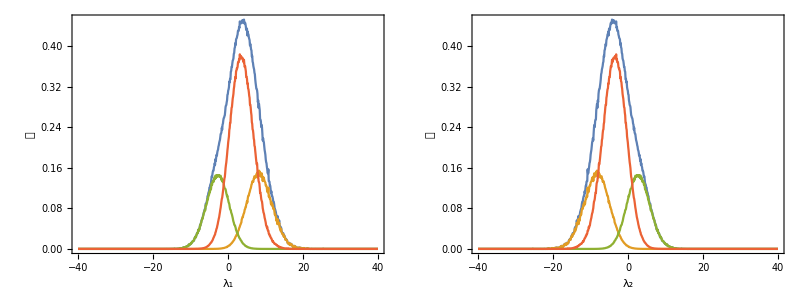

```mathematica
Grid[{{
ListLinePlot[{Ncritical,NMax,NMin,NSaddle},DataRange->{-40,40},PlotRange->All,ImageSize->300,Frame->True,FrameLabel->{"λ_1","𝒩"}],
ListLinePlot[{Ncritical⟦-1;;1;;-1⟧,NMax⟦-1;;1;;-1⟧,NMin⟦-1;;1;;-1⟧,NSaddle⟦-1;;1;;-1⟧},DataRange->{-40,40},PlotRange->All,ImageSize->300,Frame->True,FrameLabel->{"λ_2","𝒩"}]
}}]
```

```mathematica
Integrate[Abs[(T1111(T1122+(2 T122^2)/(T11-T22))-T1112^2)]π(T11-T22)p[{T11,0,T22,0,0,T122,T1111,T1112,T1122},Mtot]/.moments
,{T22,-∞,T11},{T122,-∞,∞},{T1111,-∞,∞},{T1112,-∞,∞},{T1122,-∞,∞}]
```

$Aborted

```mathematica
Integrate[Abs[T1111(T1122+(2 T122^2)/(T11-T22))-T1112^2]π(T11-T22)p[{T11,0,T22,0,0,T122,T1111,T1112,T1122},Mtot]
,{T22,-∞,T11},{T122,-∞,∞},{T1111,-∞,∞},{T1112,-∞,∞},{T1122,-∞,∞},Assumptions->{Subscript[τ, 1]>0,Subscript[τ, 2]>0,Subscript[τ, 3]>0,Subscript[τ, 4]>0}]
```

$Aborted

## Caustics

### A_3-line length

```mathematica
moments={Subscript[τ, 0]->1,Subscript[τ, 1]->1.76201,Subscript[τ, 2]->7.02844,Subscript[τ, 3]->40.1639,Subscript[τ, 4]->281.132,Subscript[τ, 5]->2257.73};
```

```mathematica
(*moments={Subscript[τ, 0]->1,Subscript[τ, 1]->1/(4 √π R),Subscript[τ, 2]->1/(8 √π R^3),Subscript[τ, 3]->3/(16 √π R^5),Subscript[τ, 4]->15/(32 √π R^7),Subscript[τ, 5]->105/(64 √π R^9)}/.R->1*)
```

```mathematica
MatrixForm[Mtot=Cov[{{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{4,0},{3,1}}]/.moments];
MatrixForm[Mmc=Cov[{{2,0},{0,2},{2,1},{1,2},{4,0},{3,1}}]/.moments];

α=1/2(pre[Mtot]/pre[Mmc]);
```

```mathematica
(*MatrixForm[Mtot=Cov[{{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{4,0},{3,1}}]];
MatrixForm[Mmc=Cov[{{2,0},{0,2},{2,1},{1,2},{4,0},{3,1}}]];
FullSimplify[(-1/2{T11, 0, T22, 0, T112, T122, T1111, T1112}.Inverse[Mtot].{T11, 0, T22, 0, T112, T122, T1111, T1112})-(-1/2{T11, T22, T112, T122, T1111, T1112}.Inverse[Mmc].{T11, T22, T112, T122, T1111, T1112})]*)
```

```mathematica
FullSimplify[Exp[(-1/2{T11, 0, T22, 0, T112, T122, T1111, T1112}.Inverse[Mtot].{T11, 0, T22, 0, T112, T122, T1111, T1112})-(-1/2{T11, T22, T112, T122, T1111, T1112}.Inverse[Mmc].{T11, T22, T112, T122, T1111, T1112})]]
```

ⅇ^(-0.000184995 T1112^2-0.00123982 T122^2)

```mathematica
Δ=0.1;
nsamples=100000000;

random=Select[RandomVariate[MultinormalDistribution[Mmc],nsamples],#⟦1⟧≥ #⟦2⟧&];
sqrt=π√((random⟦All,5⟧+(3 random⟦All,3⟧^2)/(random⟦All,1⟧-random⟦All,2⟧))^2+(random⟦All,6⟧+(3 random⟦All,3⟧ random⟦All,4⟧)/(random⟦All,1⟧-random⟦All,2⟧))^2)(random⟦All,1⟧-random⟦All,2⟧)ⅇ^(-0.0001849946675644937 random⟦All,6⟧^2-0.0012398188684266034 random⟦All,4⟧^2);
```

```mathematica
compA3L={random⟦All,1⟧,sqrt}ᵀ;
LA3=α/(Δ Length[compA3L])Total[BinLists[compA3L⟦All,1⟧->compA3L⟦All,2⟧,{-40,40,Δ}],{2}];
Clear[compA3L];
Clear[random];
```

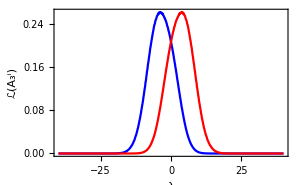

```mathematica
ListLinePlot[{LA3⟦-1;;1;;-1⟧,LA3},DataRange->{-40,40},PlotRange->All,ImageSize->300,Frame->True,FrameLabel->{"λ","ℒ(A_3^i)"},PlotStyle->{Blue,Red}]
```

### A_3-point density

```mathematica
moments={Subscript[τ, 0]->1,Subscript[τ, 1]->1.76201,Subscript[τ, 2]->7.02844,Subscript[τ, 3]->40.1639,Subscript[τ, 4]->281.132,Subscript[τ, 5]->2257.73};
```

```mathematica
MatrixForm[Mtot=Cov[{{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{4,0},{3,1},{5,0}}]];
MatrixForm[Mmc=Cov[{{2,0},{0,2},{2,1},{1,2},{4,0},{3,1},{5,0}}]];
FullSimplify[(-1/2{T11, 0, T22, 0, T112, T122, -(3 T112^2)/(T11-T22), T1112,T1111}.Inverse[Mtot].{T11, 0, T22, 0, T112, T122, -(3 T112^2)/(T11-T22), T1112,T1111})-(-1/2{T11, T22, T112, T122, T1111, T1112,T1111}.Inverse[Mmc].{T11, T22, T112, T122, T1111, T1112,T1111})]
```

64/5 (-(5 (-9 T112^4+T1111^2 (T11-T22)^2) τ_2^2)/((T11-T22)^2 (34 τ_3^4-35 τ_2^2 τ_4^2))+(4 T1112^2 τ_3^4)/(4 τ_3^4 τ_4^2-5 τ_2^2 τ_4^4))+1/τ_3^2(-2 T122^2+(16 (7 T11-T22) (T11 T1111+3 T112^2-T1111 T22) τ_3^4)/((T11-T22) (-34 τ_3^4+35 τ_2^2 τ_4^2))-((16 T1111 τ_3^2-5 T122 τ_4^2)^2)/(-125 τ_4^4+126 τ_3^2 τ_5^2)+(8 (8 T1111 τ_3^2+5 T122 τ_4^2)^2)/(-25 τ_4^4+252 τ_3^2 τ_5^2))

```mathematica
64/5 (-(5 (-9 T112^4+T1111^2 (T11-T22)^2) Subscript[τ, 2]^2)/((T11-T22)^2 (34 Subscript[τ, 3]^4-35 Subscript[τ, 2]^2 Subscript[τ, 4]^2))+(4 T1112^2 Subscript[τ, 3]^4)/(4 Subscript[τ, 3]^4 Subscript[τ, 4]^2-5 Subscript[τ, 2]^2 Subscript[τ, 4]^4))+1/Subscript[τ, 3]^2(-2 T122^2+(16 (7 T11-T22) (T11 T1111+3 T112^2-T1111 T22) Subscript[τ, 3]^4)/((T11-T22) (-34 Subscript[τ, 3]^4+35 Subscript[τ, 2]^2 Subscript[τ, 4]^2))-((16 T1111 Subscript[τ, 3]^2-5 T122 Subscript[τ, 4]^2)^2)/(-125 Subscript[τ, 4]^4+126 Subscript[τ, 3]^2 Subscript[τ, 5]^2)+(8 (8 T1111 Subscript[τ, 3]^2+5 T122 Subscript[τ, 4]^2)^2)/(-25 Subscript[τ, 4]^4+252 Subscript[τ, 3]^2 Subscript[τ, 5]^2))/.moments
```

64/5 (-T1112^2+(40 (-9 T112^4+T1111^2 (T11-T22)^2))/(53 (T11-T22)^2))+4 (-2 T122^2+(8 (7 T11-T22) (T11 T1111+3 T112^2-T1111 T22))/(53 (T11-T22))-(4 T1111-(5 T122)/4)^2/(-125/16+(63 τ_5^2)/2)+(8 (2 T1111+(5 T122)/4)^2)/(-25/16+63 τ_5^2))

```mathematica
MatrixForm[Mtot=Cov[{{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{4,0},{3,1},{5,0}}]/.moments];
MatrixForm[Mmc=Cov[{{2,0},{0,2},{2,1},{1,2},{4,0},{3,1},{5,0}}]/.moments];
FullSimplify[(-1/2{T11, 0, T22, 0, T112, T122, -(3 T112^2)/(T11-T22), T1112,T1111}.Inverse[Mtot].{T11, 0, T22, 0, T112, T122, -(3 T112^2)/(T11-T22), T1112,T1111})-(-1/2{T11, T22, T112, T122, T1111, T1112,T1111}.Inverse[Mmc].{T11, T22, T112, T122, T1111, T1112,T1111})]
```

8/265 (-424 T1112^2+60 T112^2-265 T122^2-(2880 T112^4)/(T11-T22)^2+20 (7 T11 T1111+16 T1111^2+(18 T11 T112^2)/(T11-T22)-T1111 T22))-(4 (16 T1111-5 T122)^2)/(-125+504 τ_5^2)+(32 (8 T1111+5 T122)^2)/(-25+1008 τ_5^2)

### A_4-point density

```mathematica
moments={Subscript[τ, 0]->1,Subscript[τ, 1]->1.7991650071290282,Subscript[τ, 2]->7.258798160002886,Subscript[τ, 3]->40.973950702143256,Subscript[τ, 4]->285.90540786740746,Subscript[τ, 5]->2269.103396361828};
```

```mathematica
(*moments={Subscript[τ, 0]->1,Subscript[τ, 1]->1/(4 √π R),Subscript[τ, 2]->1/(8 √π R^3),Subscript[τ, 3]->3/(16 √π R^5),Subscript[τ, 4]->15/(32 √π R^7),Subscript[τ, 5]->105/(64 √π R^9)}/.R->1*)
```

```mathematica
MatrixForm[M=Cov[{{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{4,0},{3,1},{5,0}}]/.moments]
MatrixForm[Mmc=Cov[{{2,0},{0,2},{2,1},{1,2},{3,1},{5,0}}]/.moments]
α=(pre[M]/pre[Mmc]);
```

(3/8 | 0 | 1/8 | 0 | 0 | 0 | -5/64 | 0 | 0
0 | 1/8 | 0 | 0 | 0 | 0 | 0 | -1/64 | 0
1/8 | 0 | 3/8 | 0 | 0 | 0 | -1/64 | 0 | 0
0 | 0 | 0 | 5/64 | 0 | 1/64 | 0 | 0 | -35/512
0 | 0 | 0 | 0 | 1/64 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/64 | 0 | 1/64 | 0 | 0 | -5/512
-5/64 | 0 | -1/64 | 0 | 0 | 0 | 35/512 | 0 | 0
0 | -1/64 | 0 | 0 | 0 | 0 | 0 | 5/512 | 0
0 | 0 | 0 | -35/512 | 0 | -5/512 | 0 | 0 | (63 τ_5^2)/256)

(3/8 | 1/8 | 0 | 0 | 0 | 0
1/8 | 3/8 | 0 | 0 | 0 | 0
0 | 0 | 1/64 | 0 | 0 | 0
0 | 0 | 0 | 1/64 | 0 | -5/512
0 | 0 | 0 | 0 | 5/512 | 0
0 | 0 | 0 | -5/512 | 0 | (63 τ_5^2)/256)

```mathematica
p[{T11_,T22_,T112_,T122_,T1112_,T11111_}]:=Exp[-1/2{T11,0,T22,0,T112,T122,-(3 T112^2)/(T11-T22),T1112,T11111}.Inverse[M].{T11,0,T22,0,T112,T122,-(3 T112^2)/(T11-T22),T1112,T11111}]
pmc[{T11_,T22_,T112_,T122_,T1112_,T11111_}]:=Exp[-1/2{T11,T22,T112,T122,T1112,T11111}.Inverse[Mmc].{T11,T22,T112,T122,T1112,T11111}]

p[{-0.328842,-0.360306,-0.0128047,0.0207625,-0.0430706,-0.393522}]/pmc[{-0.328842,-0.360306,-0.0128047,0.0207625,-0.0430706,-0.393522}]/.moments
```

0.807306

```mathematica
Δ=0.025;
nsamples=100000000;
nsamples=100000;

p[{T11_,T22_,T112_,T122_,T1112_,T11111_}]:=Exp[-1/2{T11,0,T22,0,T112,T122,-(3 T112^2)/(T11-T22),T1112,T11111}.Inverse[M].{T11,0,T22,0,T112,T122,-(3 T112^2)/(T11-T22),T1112,T11111}]
pmc[{T11_,T22_,T112_,T122_,T1112_,T11111_}]:=Exp[-1/2{T11,T22,T112,T122,T1112,T11111}.Inverse[Mmc].{T11,T22,T112,T122,T1112,T11111}]
```

General::munfl: Exp[-899.599] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-186401.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1992.2] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

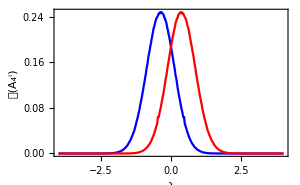

```mathematica
Monitor[NA4=Mean[Table[
random=Select[RandomVariate[MultinormalDistribution[Mmc],nsamples],#⟦1⟧≥#⟦2⟧∧RandomReal[]<p[#]/pmc[#]&];
compA4N={random⟦All,1⟧,π (random⟦All,1⟧-random⟦All,2⟧)Abs[(random⟦All,5⟧+(3 random⟦All,3⟧ random⟦All,4⟧)/(random⟦All,1⟧-random⟦All,2⟧))(random⟦All,6⟧+(random⟦All,3⟧(15random⟦All,3⟧ random⟦All,4⟧+10 random⟦All,5⟧(random⟦All,1⟧-random⟦All,2⟧)))/(random⟦All,1⟧-random⟦All,2⟧)^2)]}ᵀ;
Clear[random];

NA4=α/(Δ Length[compA4N])Total[BinLists[compA4N⟦All,1⟧->compA4N⟦All,2⟧,{-4,4,Δ}],{2}];
Clear[comopA4N];
NA4,{i,1,500}]];,i]

ListLinePlot[{NA4⟦-1;;1;;-1⟧,NA4},DataRange->{-4,4},DataRange->{-4,4},PlotRange->All,ImageSize->300,Frame->True,FrameLabel->{"λ","𝒩(A_4^i)"},PlotStyle->{Blue,Red}]
```

### D_4 points

```mathematica
moments={Subscript[τ, 0]->1,Subscript[τ, 1]->1.7991650071290282,Subscript[τ, 2]->7.258798160002886,Subscript[τ, 3]->40.973950702143256,Subscript[τ, 4]->285.90540786740746,Subscript[τ, 5]->2269.103396361828};
```

```mathematica
MatrixForm[Mtot=Cov[{{2,0},{0,2},{1,1},{3,0},{1,2},{0,3},{2,1}}]/.moments];
MatrixForm[M1=Cov[{{2,0},{0,2},{1,1}}]/.moments];
MatrixForm[Mmc=Cov[{{3,0},{1,2},{0,3},{2,1}}]/.moments];

α=(pre[Mtot]/pre[Mmc]);
```

```mathematica
nsamples=100000000;

random=RandomVariate[MultinormalDistribution[Mmc],nsamples];
det=(random⟦All,4⟧-random⟦All,3⟧)random⟦All,4⟧-(random⟦All,1⟧-random⟦All,2⟧)random⟦All,2⟧;
Clear[random];
```

```mathematica
D4[ν_]=α Exp[-1/2{ν,ν,0}.Inverse[M1].{ν,ν,0}]Mean[Abs[det]];
D4P[ν_]=α Exp[-1/2{ν,ν,0}.Inverse[M1].{ν,ν,0}]Mean[HeavisideTheta[det]Abs[det]];
D4M[ν_]=α Exp[-1/2{ν,ν,0}.Inverse[M1].{ν,ν,0}]Mean[HeavisideTheta[-det]Abs[det]];
Clear[det]
```

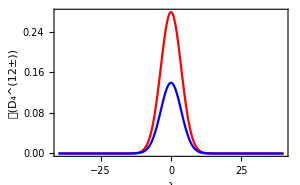

```mathematica
Plot[{D4[ν],D4P[ν]},{ν,-40,40},PlotStyle->{Red,(*Green,*)Blue},ImageSize->300,Frame->True,FrameLabel->{"λ","𝒩(D_4^(12±))"},PlotRange->All]
```

```mathematica
moments={Subscript[τ, 0]->1,Subscript[τ, 1]->1.76201,Subscript[τ, 2]->7.02844,Subscript[τ, 3]->40.1639,Subscript[τ, 4]->281.132,Subscript[τ, 5]->2257.73};
MatrixForm[Mmc=Cov[{{3,0},{1,2},{0,3},{2,1}}]/.moments]
```

(504.106 | 100.821 | 0 | 0
100.821 | 100.821 | 0 | 0
0 | 0 | 504.106 | 100.821
0 | 0 | 100.821 | 100.821)

```mathematica
nsamples=100000000;

random=RandomVariate[MultinormalDistribution[Mmc],nsamples];
det=(random⟦All,4⟧-random⟦All,3⟧)random⟦All,4⟧-(random⟦All,1⟧-random⟦All,2⟧)random⟦All,2⟧;
Clear[random];
```

```mathematica
Mean[Abs[det]]
Mean[HeavisideTheta[det]Abs[det]]
Mean[HeavisideTheta[-det]Abs[det]]
```

201.634

100.814

100.82

```mathematica
FullSimplify[(-1/2{T111,T112,T122,T222}.Inverse[Cov[{{3,0},{2,1},{1,2},{0,3}}]].{T111,T112,T122,T222})-(-1/2{T222,T122,T112,T111}.Inverse[Cov[{{3,0},{2,1},{1,2},{0,3}}]].{T222,T122,T112,T111})]
```

0

## Test

```mathematica
Beep[]
```